```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Edetect={1 10^-8,2.5 10^-8,1 10^-7,2 10^-7,3 10^-7,4 10^-7,5 10^-7,6 10^-7,8 10^-7,1 10^-6,3.16 10^-6,1 10^-5,1 10^-4,1 10^-3,1 10^-2};
pointfiles={
"prevLPemissionPoints_e01.tst",
"prevLPemissionPoints_e02.tst",
"prevLPemissionPoints_e03.tst",
"prevLPemissionPoints_e04.tst",
"prevLPemissionPoints_e05.tst",
"prevLPemissionPoints_e06.tst",
"prevLPemissionPoints_e07.tst",
"prevLPemissionPoints_e08.tst",
"prevLPemissionPoints_e09.tst",
"prevLPemissionPoints_e10.tst",
"prevLPemissionPoints_e11.tst",
"prevLPemissionPoints_e12.tst",
"prevLPemissionPoints_e13.tst",
"prevLPemissionPoints_e14.tst",
"prevLPemissionPoints_e15.tst"
};
tracefiles={
"prevLPemissionPoints_e01_traces.tst",
"prevLPemissionPoints_e02_traces.tst",
"prevLPemissionPoints_e03_traces.tst",
"prevLPemissionPoints_e04_traces.tst",
"prevLPemissionPoints_e05_traces.tst",
"prevLPemissionPoints_e06_traces.tst",
"prevLPemissionPoints_e07_traces.tst",
"prevLPemissionPoints_e08_traces.tst",
"prevLPemissionPoints_e09_traces.tst",
"prevLPemissionPoints_e10_traces.tst",
"prevLPemissionPoints_e11_traces.tst",
"prevLPemissionPoints_e12_traces.tst",
"prevLPemissionPoints_e13_traces.tst",
"prevLPemissionPoints_e14_traces.tst",
"prevLPemissionPoints_e15_traces.tst"
};
mapfiles={
"LPemissionMap_e01.tst",
"LPemissionMap_e02.tst",
"LPemissionMap_e03.tst",
"LPemissionMap_e04.tst",
"LPemissionMap_e05.tst",
"LPemissionMap_e06.tst",
"LPemissionMap_e07.tst",
"LPemissionMap_e08.tst",
"LPemissionMap_e09.tst",
"LPemissionMap_e10.tst",
"LPemissionMap_e11.tst",
"LPemissionMap_e12.tst",
"LPemissionMap_e13.tst",
"LPemissionMap_e14.tst",
"LPemissionMap_e15.tst"
};
rMoon=1737;
aMoon=0.3844 10^6;
mMoon=0.07346 10^24;
mEarth=5.9724 10^24;
rSOImoon=aMoon(mMoon/mEarth)^(2/5);
p=250;
{vp,vv}=Options[Graphics3D,{ViewPoint,ViewVertical}][[All,2]];
a=Table[ReadList[pointfiles[[i]],Number,RecordLists->True],{i,1,Length[pointfiles],1}];
b=Table[Partition[ReadList[tracefiles[[i]],Number,RecordLists->True],11],{i,1,Length[tracefiles],1}];
c=Table[ReadList[mapfiles[[i]],Number,RecordLists->True],{i,1,Length[mapfiles],1}];
```

```mathematica
origin={0,0,0};
Dhat=a[[1,1,9;;11]];
Nhat=a[[1,1,12;;14]];
Fhat=a[[1,1,15;;17]];
Rsat=a[[1,1,3;;5]];
rView=Norm[Rsat];
r1s=a[[;;,;;,5;;7]];
v1s=a[[;;,;;,8;;10]];
arrDs=a[[;;,;;,1;;3]];
v2s=b[[;;,;;,11,5;;7]];
traces=b[[;;,;;,;;,2;;4]];
lenA=Table[Length[a[[i]]],{i,1,Length[a]}];
lenB=Table[Length[b[[i]]],{i,1,Length[b]}];
trips=Flatten[traces,2];
rMaxs=Table[Max[Table[Norm[Flatten[traces[[j]],1][[i]]],{i,1,lenB[[j]]}]],{j,1,Length[tracefiles],1}];
```

```mathematica
Manipulate[
If[j>k,k=j];
If[k>lenB[[En]],k=lenB[[En]]];
If[r>rMaxs[[En]],r=rMaxs[[En]]];
Grid[{{
Show[ListPointPlot3D[
{
Table[a[[En,1,3;;5]]+p a[[En,i,1;;3]],{i,2,Length[a[[En,2;;]]],1}],
a[[En,2;;,5;;7]]
},
PlotStyle->{Directive[Gray,PointSize[0.001]],Directive[Black,PointSize[0.004]]},PlotRange->Table[{-r,r},3],BoxRatios->1,ImageSize->720,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv],PlotLabel->"En at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15r Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15r Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15r Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9r{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9r{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9r{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}],
Graphics3D[{Green,Line[traces[[En,j;;k]]]}],
Table[Graphics3D[{Orange,Arrowheads[.01],Arrow[{r1s[[En,i]],r1s[[En,i]]+.05r v1s[[En,i]]}]}],{i,j+1,k+1,1}]
],
Grid[{
{Show[ListPointPlot3D[
a[[En,2;;,1;;3]],
PlotStyle->Directive[Gray,PointSize[0.007]],PlotRange->{-1,1},BoxRatios->1,ImageSize->360,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]],
Graphics3D[{Black,Arrowheads[.02],Arrow[{origin,Dhat}]}],
Graphics3D[{Blue,Arrowheads[.02],Arrow[{origin,Nhat}]}],
Graphics3D[{Red,Arrowheads[.02],Arrow[{origin,Fhat}]}],
Table[Graphics3D[{Darker[Green],PointSize[0.01],Point[arrDs[[En,i]]]}],{i,j+1,k+1,1}],
Table[Graphics3D[{Darker[Green],Arrow[{arrDs[[En,i]],origin}]}],{i,j+1,k+1,1}],
Table[Graphics3D[{Green,Arrow[{-v2s[[En,i]],origin}]}],{i,j,k,1}]
]},
{Show[ListPointPlot3D[
a[[En,2;;,5;;7]],
PlotStyle->{Directive[Black,PointSize[0.007]]},PlotRange->Table[1.25rMoon{-1,1},3],BoxRatios->1,ImageSize->360,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]],
Graphics3D[{LightGray,Arrowheads[.03],Arrow[{origin,1.2rMoon{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.03],Arrow[{origin,1.2rMoon{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.03],Arrow[{origin,1.2rMoon{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}],
Table[Graphics3D[{Orange,Arrowheads[.02],Arrow[{r1s[[En,i]],r1s[[En,i]]+.1rMoon v1s[[En,i]]}]}],{i,j+1,k+1,1}]
]}
},Frame->{{False,False},{False,True}}]
}},Frame->All],
{{En,1},1,Length[lenA],1,Appearance->{"Open"}},
{{j,1},1,lenB[[En]],1,Appearance->{"Open"}},
{{k,Max[lenB]},j,Max[lenB],1,Appearance->{"Open"}},
{{r,rSOImoon},rView,rSOImoon,(rSOImoon-Norm[Rsat])/100,Appearance->{"Open"}},
ContinuousAction->False,ControlPlacement->Left
]
```

```mathematica
padding={{72,48},{36,20}};
tofEnpairs=Table[Partition[Riffle[a[[En,2;;,4]],a[[En,2;;,11]]/1000],2],{En,1,Length[a],1}];
tofDpairs=Table[Partition[Riffle[a[[En,2;;,4]],a[[En,2;;,12]]],2],{En,1,Length[a],1}];
Manipulate[
Overlay[{
ListLogLogPlot[tofEnpairs[[En]],ImageSize->Large,PlotStyle->Blue,Frame->{{True,False},{True,True}},FrameTicks->{{True,False},{True,False}},FrameStyle->{{Blue,None},{Black,Black}},FrameLabel->{{"En [keV]",None},{"tof [s]","En at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"}},ImagePadding->padding],
ListLogLogPlot[tofDpairs[[En]],ImageSize->Large,PlotStyle->Red,Frame->{{False,True},{False,False}},FrameTicks->True,FrameStyle->{{None,Red},{None,None}},FrameLabel->{{None,"D-factor"},{None,None}},ImagePadding->padding]
},Alignment->Center],
{En,1,Length[a],1,Appearance->{"Open"}}]
```

```mathematica
EnIpairs=Table[Partition[Riffle[a[[En,2;;,11]]/1000,2376/(a[[En,2;;,12]] ⅇ^(-a[[En,2;;,4]]/L))],2],{En,1,Length[a],1}];
Manipulate[
If[m1≥m2,m2=m1+1];
ListLogLogPlot[EnIpairs[[En]]/.L->Ln,ImageSize->Large,PlotRange->{All,{10^m1,10^m2}},PlotStyle->Blue,Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{{"I [n-surface per n-detector]",None},{"En [MeV]","En at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"}}],
{En,1,Length[a],1,Appearance->{"Open"}},
{{Ln,881},875,895,0.5,Appearance->{"Open"}},
{{m1,9},1,60,1,Appearance->{"Open"}},
{{m2,15},1,60,1,Appearance->{"Open"}},
ControlPlacement->Right]
```

```mathematica
latTicks=Table[i,{i,-90,90,15}];
lonTicks=Table[i,{i,-180,180,30}];
spread=2.5;
LonLatRect5[xy_]:=Rectangle[xy-spread,xy+spread];
```

```mathematica
CmapTriplets=Table[c[[En,2;;,{2,1,18}]],{En,1,Length[c],1}];
CmapTriplets[[;;,;;,3]]=Table[CmapTriplets[[En,;;,3]]/Max[CmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Cmap2lists=Table[Table[{CmapTriplets[[En,i,1;;2]]},{i,1,Length[CmapTriplets[[En,;;,3]]],1}],{En,1,Length[CmapTriplets],1}];
CmapColors=Table[Table[ColorData["Rainbow"][CmapTriplets[[En,i,3]]],{i,1,Length[CmapTriplets[[En,;;,3]]],1}],{En,1,Length[CmapTriplets],1}];
CmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"RELATIVE NUMBER OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{CmapColors[[En,i]],Point[CmapVecs[[En,i]]]},{i,1,Length[CmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[BarLegend["Rainbow"],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],CmapColors[[En,i]],LonLatRect5[Flatten[Cmap2lists[[En,i]]]]}],{i,1,Length[Cmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[CmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
FmapTriplets=Table[c[[En,2;;,{2,1,6}]],{En,1,Length[c],1}];
FErrmapTriplets=Table[c[[En,2;;,{2,1,7}]],{En,1,Length[c],1}];
FErrmapTriplets[[;;,;;,3]]=100(Abs[FErrmapTriplets[[;;,;;,3]]]/FmapTriplets[[;;,;;,3]]);
FmapTriplets[[;;,;;,3]]=Table[FmapTriplets[[En,;;,3]]/Max[FmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Fmap2lists=Table[Table[{FmapTriplets[[En,i,1;;2]]},{i,1,Length[FmapTriplets[[En,;;,3]]],1}],{En,1,Length[FmapTriplets],1}];
FmapColors=Table[Table[ColorData["Rainbow"][FmapTriplets[[En,i,3]]],{i,1,Length[FmapTriplets[[En,;;,3]]],1}],{En,1,Length[FmapTriplets],1}];
FmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][FErrmapTriplets[[En,i,3]]/100],{i,1,Length[FErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[FErrmapTriplets],1}];
FmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"RELATIVE WEIGHT (BY DIVERGENCE) OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{FmapColors[[En,i]],Point[FmapVecs[[En,i]]]},{i,1,Length[FmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[BarLegend["Rainbow"],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FmapColors[[En,i]],LonLatRect5[Flatten[Fmap2lists[[En,i]]]]}],{i,1,Length[Fmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FmapErrColors[[En,i]],LonLatRect5[Flatten[Fmap2lists[[En,i]]]]}],{i,1,Length[Fmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[FmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[FErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
FtmapTriplets=Table[c[[En,2;;,{2,1,8}]],{En,1,Length[c],1}];
FtErrmapTriplets=Table[c[[En,2;;,{2,1,9}]],{En,1,Length[c],1}];
FtErrmapTriplets[[;;,;;,3]]=100(Abs[FtErrmapTriplets[[;;,;;,3]]]/FtmapTriplets[[;;,;;,3]]);
FtmapTriplets[[;;,;;,3]]=Table[FtmapTriplets[[En,;;,3]]/Max[FtmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Ftmap2lists=Table[Table[{FtmapTriplets[[En,i,1;;2]]},{i,1,Length[FtmapTriplets[[En,;;,3]]],1}],{En,1,Length[FtmapTriplets],1}];
FtmapColors=Table[Table[ColorData["Rainbow"][FtmapTriplets[[En,i,3]]],{i,1,Length[FtmapTriplets[[En,;;,3]]],1}],{En,1,Length[FtmapTriplets],1}];
FtmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][FtErrmapTriplets[[En,i,3]]/100],{i,1,Length[FtErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[FtErrmapTriplets],1}];
FtmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"RELATIVE WEIGHT (BY DIVERGENCE AND DECAY) OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{FmapColors[[En,i]],Point[FtmapVecs[[En,i]]]},{i,1,Length[FtmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[BarLegend["Rainbow"],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FtmapColors[[En,i]],LonLatRect5[Flatten[Ftmap2lists[[En,i]]]]}],{i,1,Length[Ftmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FtmapErrColors[[En,i]],LonLatRect5[Flatten[Ftmap2lists[[En,i]]]]}],{i,1,Length[Ftmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[FtmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[FtErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
TmapTriplets=Table[c[[En,2;;,{2,1,10}]],{En,1,Length[c],1}];
Tmax=Table[Max[TmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
TErrmapTriplets=Table[c[[En,2;;,{2,1,11}]],{En,1,Length[c],1}];
TErrmapTriplets[[;;,;;,3]]=100(Abs[TErrmapTriplets[[;;,;;,3]]]/TmapTriplets[[;;,;;,3]]);
TmapTriplets[[;;,;;,3]]=Table[TmapTriplets[[En,;;,3]]/Max[TmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Tmap2lists=Table[Table[{TmapTriplets[[En,i,1;;2]]},{i,1,Length[TmapTriplets[[En,;;,3]]],1}],{En,1,Length[TmapTriplets],1}];
TmapColors=Table[Table[ColorData["Rainbow"][TmapTriplets[[En,i,3]]],{i,1,Length[TmapTriplets[[En,;;,3]]],1}],{En,1,Length[TmapTriplets],1}];
TmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][TErrmapTriplets[[En,i,3]]/100],{i,1,Length[TErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[TErrmapTriplets],1}];
TmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"TIME OF FLIGHT OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{TmapColors[[En,i]],Point[TmapVecs[[En,i]]]},{i,1,Length[TmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","TOF"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Tmax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],TmapColors[[En,i]],LonLatRect5[Flatten[Tmap2lists[[En,i]]]]}],{i,1,Length[Tmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],TmapErrColors[[En,i]],LonLatRect5[Flatten[Tmap2lists[[En,i]]]]}],{i,1,Length[Tmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[TmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","TOF"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[TErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
Table[Max[Table[c[[En,2;;,10]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Mean[Table[c[[En,2;;,10]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Min[Table[c[[En,2;;,10]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
```

{547639.,516673.,731.216,451.439,351.082,295.676,259.984,234.458,199.567,176.731,95.5634,52.6752,16.3825,5.15364,1.62602}

{79323.4,25443.7,531.003,335.504,265.224,225.673,199.657,180.698,154.943,137.729,75.6905,42.0637,13.1893,4.15595,1.31314}

{1900.77,593.801,277.255,191.345,154.702,133.228,118.597,107.814,92.8365,82.7163,45.8922,25.6054,8.0456,2.53921,0.802466}

```mathematica
EmapTriplets=Table[c[[En,2;;,{2,1,12}]],{En,1,Length[c],1}];
Emax=Table[Max[EmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
EErrmapTriplets=Table[c[[En,2;;,{2,1,13}]],{En,1,Length[c],1}];
EErrmapTriplets[[;;,;;,3]]=100(Abs[EErrmapTriplets[[;;,;;,3]]]/EmapTriplets[[;;,;;,3]]);
EmapTriplets[[;;,;;,3]]=Table[EmapTriplets[[En,;;,3]]/Max[EmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Emap2lists=Table[Table[{EmapTriplets[[En,i,1;;2]]},{i,1,Length[EmapTriplets[[En,;;,3]]],1}],{En,1,Length[EmapTriplets],1}];
EmapColors=Table[Table[ColorData["Rainbow"][EmapTriplets[[En,i,3]]],{i,1,Length[EmapTriplets[[En,;;,3]]],1}],{En,1,Length[EmapTriplets],1}];
EmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][EErrmapTriplets[[En,i,3]]/100],{i,1,Length[EErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[EErrmapTriplets],1}];
EmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"EMISSION ENERGY OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{EmapColors[[En,i]],Point[EmapVecs[[En,i]]]},{i,1,Length[EmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Ee"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Emax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],EmapColors[[En,i]],LonLatRect5[Flatten[Emap2lists[[En,i]]]]}],{i,1,Length[Emap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],EmapErrColors[[En,i]],LonLatRect5[Flatten[Emap2lists[[En,i]]]]}],{i,1,Length[Emap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[EmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Ee"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[EErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
Table[Max[Table[c[[En,2;;,12]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Mean[Table[c[[En,2;;,12]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Min[Table[c[[En,2;;,12]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
```

{0.0000287472,0.0000425668,0.000125183,0.00023248,0.000338261,0.000443177,0.000547601,0.000651183,0.000858193,0.00106438,0.00327022,0.0101921,0.100597,1.00188,10.0059}

{0.000022621,0.0000221377,0.0000820129,0.000173831,0.00026618,0.000359875,0.000454374,0.000549027,0.000740124,0.00093211,0.00303458,0.0097716,0.0992587,0.997646,9.99254}

{0.000012642,0.0000157653,0.0000652521,0.000145193,0.000229735,0.000316689,0.000405186,0.000494779,0.000676295,0.000860002,0.00289989,0.00952588,0.0984688,0.995126,9.98455}

```mathematica
ZmapTriplets=Table[c[[En,2;;,{2,1,14}]],{En,1,Length[c],1}];
Zmax=Table[Max[ZmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
ZErrmapTriplets=Table[c[[En,2;;,{2,1,15}]],{En,1,Length[c],1}];
ZErrmapTriplets[[;;,;;,3]]=100(Abs[ZErrmapTriplets[[;;,;;,3]]]/ZmapTriplets[[;;,;;,3]]);
ZmapTriplets[[;;,;;,3]]=Table[ZmapTriplets[[En,;;,3]]/Max[ZmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Zmap2lists=Table[Table[{ZmapTriplets[[En,i,1;;2]]},{i,1,Length[ZmapTriplets[[En,;;,3]]],1}],{En,1,Length[ZmapTriplets],1}];
ZmapColors=Table[Table[ColorData["Rainbow"][ZmapTriplets[[En,i,3]]],{i,1,Length[ZmapTriplets[[En,;;,3]]],1}],{En,1,Length[ZmapTriplets],1}];
ZmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][ZErrmapTriplets[[En,i,3]]/100],{i,1,Length[ZErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[ZErrmapTriplets],1}];
ZmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"DIVERGENCE AFTER EMISSION OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{ZmapColors[[En,i]],Point[ZmapVecs[[En,i]]]},{i,1,Length[ZmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","DF"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Zmax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],ZmapColors[[En,i]],LonLatRect5[Flatten[Zmap2lists[[En,i]]]]}],{i,1,Length[Zmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],ZmapErrColors[[En,i]],LonLatRect5[Flatten[Zmap2lists[[En,i]]]]}],{i,1,Length[Zmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[ZmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","DF"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[ZErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
DmapTriplets=Table[c[[En,2;;,{2,1,16}]],{En,1,Length[c],1}];
Dmax=Table[Max[DmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
DErrmapTriplets=Table[c[[En,2;;,{2,1,17}]],{En,1,Length[c],1}];
DErrmapTriplets[[;;,;;,3]]=100(Abs[DErrmapTriplets[[;;,;;,3]]]/DmapTriplets[[;;,;;,3]]);
DmapTriplets[[;;,;;,3]]=Table[DmapTriplets[[En,;;,3]]/Max[DmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Dmap2lists=Table[Table[{DmapTriplets[[En,i,1;;2]]},{i,1,Length[DmapTriplets[[En,;;,3]]],1}],{En,1,Length[DmapTriplets],1}];
DmapColors=Table[Table[ColorData["Rainbow"][DmapTriplets[[En,i,3]]],{i,1,Length[DmapTriplets[[En,;;,3]]],1}],{En,1,Length[DmapTriplets],1}];
DmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][DErrmapTriplets[[En,i,3]]/100],{i,1,Length[DErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[DErrmapTriplets],1}];
DmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"DIVERGENCE AFTER EMISSION OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{DmapColors[[En,i]],Point[DmapVecs[[En,i]]]},{i,1,Length[DmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","DF"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Dmax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],DmapColors[[En,i]],LonLatRect5[Flatten[Dmap2lists[[En,i]]]]}],{i,1,Length[Dmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],DmapErrColors[[En,i]],LonLatRect5[Flatten[Dmap2lists[[En,i]]]]}],{i,1,Length[Dmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[DmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","DF"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[DErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
d=ReadList["E_fluence-test-decay.tst",Number,RecordLists->True];
dNoDecay=ReadList["E_fluence-test-nodecay.tst",Number,RecordLists->True];
```

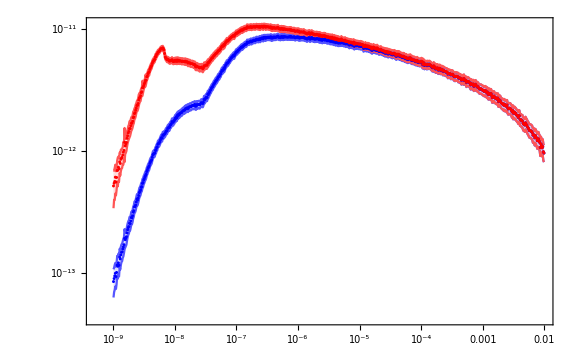

```mathematica
EspecPairs=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]],2];
EspecPairsErrt=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]+6d[[;;,6]]],2];
EspecPairsErrb=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]-6d[[;;,6]]],2];
EndspecPairs=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]],2];
EndspecPairsErrt=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]+6dNoDecay[[;;,6]]],2];
EndspecPairsErrb=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]-6dNoDecay[[;;,6]]],2];
ListLogLogPlot[{EspecPairs,EspecPairsErrt,EspecPairsErrb,EndspecPairs,EndspecPairsErrt,EndspecPairsErrb},ImageSize->Large,Frame->True,Joined->{False,True,True,False,True,True},Filling->{2->{3},5->{6}},PlotStyle->{Blue,Lighter[Blue],Lighter[Blue],Red,Lighter[Red],Lighter[Red]},GridLines->All]
```

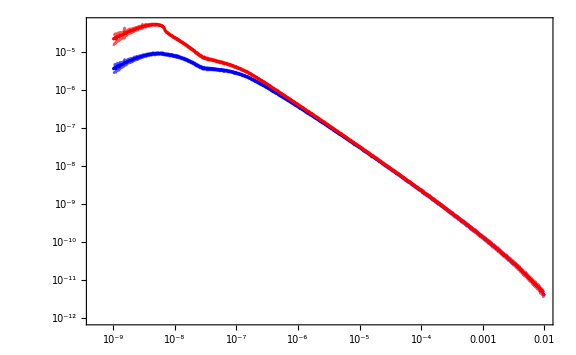

```mathematica
EspecPairs=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]/(d[[;;,3]]-d[[;;,2]])],2];
EspecPairsErrt=Partition[Riffle[d[[;;,4]]/1000,(d[[;;,5]]+6d[[;;,6]])/(d[[;;,3]]-d[[;;,2]])],2];
EspecPairsErrb=Partition[Riffle[d[[;;,4]]/1000,(d[[;;,5]]-6d[[;;,6]])/(d[[;;,3]]-d[[;;,2]])],2];
EndspecPairs=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]/(dNoDecay[[;;,3]]-dNoDecay[[;;,2]])],2];
EndspecPairsErrt=Partition[Riffle[dNoDecay[[;;,4]]/1000,(dNoDecay[[;;,5]]+6dNoDecay[[;;,6]])/(dNoDecay[[;;,3]]-dNoDecay[[;;,2]])],2];
EndspecPairsErrb=Partition[Riffle[dNoDecay[[;;,4]]/1000,(dNoDecay[[;;,5]]-6dNoDecay[[;;,6]])/(dNoDecay[[;;,3]]-dNoDecay[[;;,2]])],2];
ListLogLogPlot[{EspecPairs,EspecPairsErrt,EspecPairsErrb,EndspecPairs,EndspecPairsErrt,EndspecPairsErrb},ImageSize->Large,Frame->True,Joined->{False,True,True,False,True,True},Filling->{2->{3},5->{6}},PlotStyle->{Blue,Lighter[Blue],Lighter[Blue],Red,Lighter[Red],Lighter[Red]},GridLines->All]
```

```mathematica
Edetect[[1]]//N
```

1.×10^-8

```mathematica
Position[Partition[Riffle[d[[;;,2]]/1000,d[[;;,5]]/(d[[;;,3]]-d[[;;,2]])],2],Table[EspecPairs[[i,1]]>Edetect[[1]],{i,1,Length[EspecPairs[[;;,1]]],1}]]
```

{}

```mathematica
p0=4.4598`100 10^6;
p1=3.6840`100 10^-8;
p2=4.4183`100 10^5;
p3=0.9181`100;
p4=1.4567`100 10^-7;
p5=5.0338`100;
s[x_]=p0/p1 x ⅇ^(-x/p1)+(p2(x/p4)^p5(p4/x)^p3)/(1+(x/p4)^p5);
AD[x_]=Cos[x]^(5/4);
EePDF[Ee_]=FullSimplify[s[Ee]/NIntegrate[s[Ee],{Ee,10^-9,10^-2},WorkingPrecision->90,AccuracyGoal->20,PrecisionGoal->20]]
AePDF[θ_]=FullSimplify[AD[θ]/NIntegrate[AD[θ],{θ,0,π/2},WorkingPrecision->90,AccuracyGoal->20,PrecisionGoal->20]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ee near {Ee} = {5.7063238008294073156466006414391865388511528162115454113623781646636748130348081119292234700436458438197579319512284902215099005151071792466×10^-7}. NIntegrate obtained 1.3344610093645871403935540714042466190968395051356788117609984285027064013174767147991814862891318014196514687538730814765112251855760555631 and 2.1103863142228105441007414065740519965419487637338683484451812721612365817513300663752071606510474931886214281276510996083051225557510663245×10^-13 for the integral and error estimates.

9.07172491907178396755348082384732845415722023656074800040861900501772392123073231588192615×10^13 ⅇ^(-2.714440825190010857763300760043431053203040173724212812160694896851248642779587404994571118349619978×10^7 Ee) Ee+(4.5442990972019588147496187052277537233204258554897045691209833561745694147011879999948981×10^33 (1/Ee)^0.9181 Ee^5.0338)/(1+2.5955385812264932799677304301611234049501854921236982365409503231874408604901244718921545918507349×10^34 Ee^5.0338)

1.07425917878735074884995016222072182268037256860695708903071702049044345022681759726806329 Cos[θ]^(5/4)

```mathematica
CountIntensities=Table[c[[En,2;;,18]]/(c[[En,1,-1]]+c[[En,1,-2]]),{En,1,Length[c],1}];
EeIntensities=Table[EePDF[c[[En,2;;,12]]],{En,1,Length[c],1}];
AeIntensities=Table[AePDF[ArcCos[c[[En,2;;,14]]]],{En,1,Length[c],1}];
DIntensities=Table[c[[En,2;;,16]],{En,1,Length[c],1}];
tIntensities=Table[ⅇ^(-c[[En,2;;,10]]/(611/Log[2])),{En,1,Length[c],1}];
```

```mathematica
Table[Total[CountIntensities[[En]]],{En,1,Length[c],1}]//N
```

{0.334,0.199939,0.0987097,0.0976325,0.0979477,0.0983357,0.0986922,0.0989935,0.0994962,0.0998795,0.101531,0.102654,0.103771,0.104132,0.104261}

```mathematica
Table[(c[[En,1,-1]]+c[[En,1,-2]]),{En,1,Length[c],1}]/Total[Table[(c[[En,1,-1]]+c[[En,1,-2]]),{En,1,Length[c],1}]]//N
```

{0.02178,0.0363836,0.073696,0.0745091,0.0742693,0.0739763,0.073709,0.0734847,0.0731134,0.0728329,0.0716483,0.0708647,0.0701017,0.0698588,0.0697723}

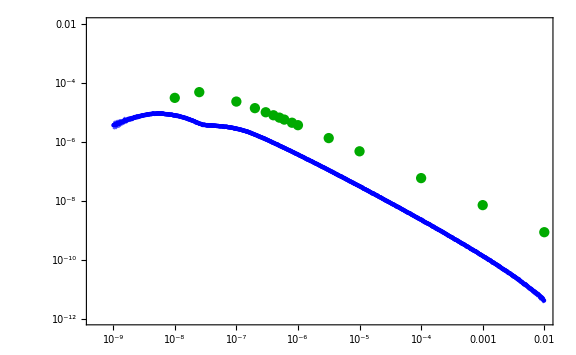

```mathematica
Show[
ListLogLogPlot[{EspecPairs,EspecPairsErrt,EspecPairsErrb},ImageSize->Large,Frame->True,Joined->{False,True,True},Filling->{2->{3}},PlotStyle->{Blue,Lighter[Blue],Lighter[Blue]},GridLines->All,PlotRange->{10^-12,10^-2}],
ListLogLogPlot[Partition[Riffle[Edetect,Table[Total[CountIntensities[[En]] EeIntensities[[En]] AeIntensities[[En]] DIntensities[[En]] tIntensities[[En]]],{En,1,Length[c],1}]],2],PlotStyle->Darker[Green]]
]
```

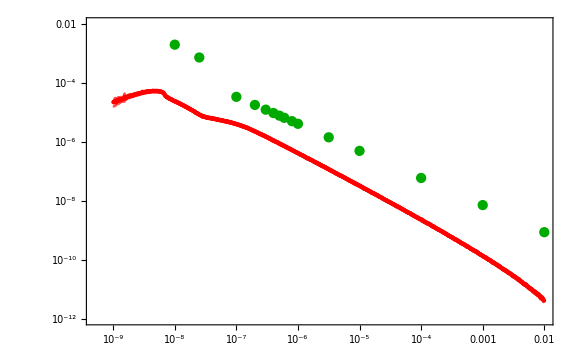

```mathematica
Show[
ListLogLogPlot[{EndspecPairs,EndspecPairsErrt,EndspecPairsErrb},ImageSize->Large,Frame->True,Joined->{False,True,True},Filling->{2->{3}},PlotStyle->{Red,Lighter[Red],Lighter[Red]},GridLines->All,PlotRange->{10^-12,10^-2}],
ListLogLogPlot[Partition[Riffle[Edetect,Table[Total[CountIntensities[[En]] EeIntensities[[En]] AeIntensities[[En]] DIntensities[[En]]],{En,1,Length[c],1}]],2],PlotStyle->Darker[Green]]
]
```